## Load Freezeout Data

```mathematica
ClearAll["Global`*"]
fodata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOutCorrected.csv"]];
headers=fodata[[1]]
fofields=Transpose@fodata[[2;;]];
αs=fofields[[1]];
τs=fofields[[2]];
rs=fofields[[3]];
Dτs=fofields[[4]];
Drs=fofields[[5]];
urs=fofields[[6]];
uτs=fofields[[7]];
```

{alpha,tau,r,Dtau,Dr,ur,utau}

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
```

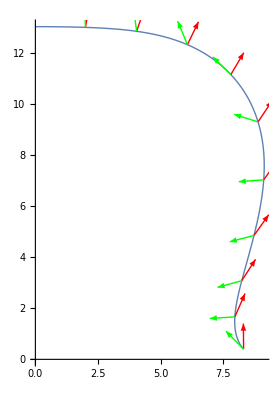

```mathematica
u[α_]=1/Sqrt[ur[α]^2+uτ[α]^2]*{ur[α],uτ[α]};
n[α_]=1/Sqrt[Dτ[α]^2+Dr[α]^2]*{Dτ[α],Dr[α]};
curve[α_]:={r[α],τ[α]};
ParametricPlot[
curve[α],{α,0,π/2},PlotStyle->Thick,
Epilog->{
{
Red,Thick,Arrow[{curve@#,curve@#+u@#}]&/@Rest[Subdivide[0,Pi/2,10]]
},
{
Green,Thick,Arrow[{curve@#,curve@#+n@#}]&/@Rest[Subdivide[0,Pi/2,10]]
}},
PlotRange->Automatic]
```

## Define Spectrum Computation

```mathematica
ComputeJp[m_,ps_,f_,Df_,anti_]:=Module[{ωs,J0rp,J1rp,Y0tw,Y1tw,J0tw,J1tw,plusminus,G0,G1,Jp},
(*
f is supposed to be the condensate field, Df it's perpendicular derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]
*)
ωs=Sqrt[ps^2+m^2];(*in GeV (p in GeV) *)
J0rp[α_]=BesselJ[0,r[α]*ps*GeVtoIfm];(*dimensionless*)
J1rp[α_]=BesselJ[1,r[α]*ps*GeVtoIfm];(*dimensionless*)
Y0tw[α_]=BesselY[0,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
Y1tw[α_]=BesselY[1,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
J0tw[α_]=BesselJ[0,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
J1tw[α_]=BesselJ[1,τ[α]*ωs*GeVtoIfm];(*dimensionless*)

plusminus=If[anti,-1,+1];

G0[α_]=J0rp[α]*(-Y0tw[α]+plusminus*I*J0tw[α]);(*dimensionless*)
G1[α_]=Dτ[α]*fmtoIGeV*ps*J1rp[α]*(-Y0tw[α]+plusminus*I*J0tw[α])+(*dimensionless*)
Dr[α]*fmtoIGeV*ωs*J0rp[α]*(-Y1tw[α]+plusminus*I*J1tw[α]);(*dimensionless*)

Jp=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0[α]+f[α]*G1[α]),{α,0,π/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
Jp
]
```

## Compute the spectrum for some initial data set

Browse the local filesystem for initial data and copy/paste the desired directory to the Import statement. Typically, each folder contains multiple files with initial data labeled “initXX.csv”.

```mathematica
FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/init*"]]
```

{/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_comp_constfield_m140_varphase_20250116_120129,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_comp_constfield_m140_varphase_20250117_181049,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_comp_constfield_m140_varphase_20250117_181304,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_real_consteps_m140_20250117_113521,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_real_consteps_varm_20250116_114850,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_real_constfield_m140_20250116_115949,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/init_real_taudep_m140_20250117_162422}

{{# 20250116_115949},{# epsilon:0.00012298(GeV^4)},{# mass:0.14(GeV)},{# sign:1},{alpha,RePhi,ImPhi,ReDPhi,ImDPhi}}

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.533599,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[1.0572,#~~___].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

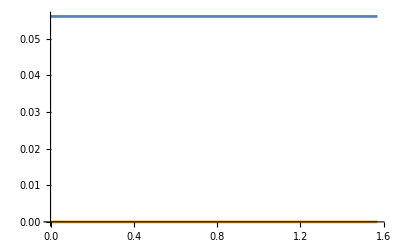

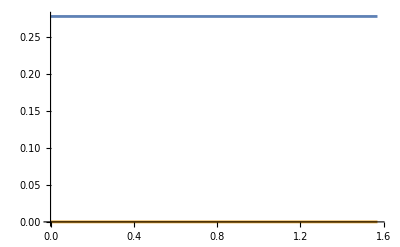

```mathematica
initdata=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/init_real_consteps_varm_20250116_114850/init10.csv"],"CSV"];
initdata[[1;;5]]
initdatatemp=DeleteCases[initdata,_?(StringMatchQ[#[[1]],"#"~~___]&)];
fieldheader=initdatatemp[[1]];
αfields=Transpose[initdatatemp[[2;;]]][[1]];
fieldRes=Transpose[initdatatemp[[2;;]]][[2]];
fieldIms=Transpose[initdatatemp[[2;;]]][[3]];
dfieldRes=Transpose[initdatatemp[[2;;]]][[4]];
dfieldIms=Transpose[initdatatemp[[2;;]]][[5]];

ϕ=Interpolation[Transpose@{αfields,fieldRes+I*fieldIms}];
Dϕ=Interpolation[Transpose@{αfields,dfieldRes+I*dfieldIms}];
Plot[{Re@ϕ[α],Im@ϕ[α]},{α,0,π/2}]
Plot[{Re@Dϕ[α],Im@Dϕ[α]},{α,0,π/2}]
```

Define the desired momentum grid and compute spectrum and antispectrum . For real fields the particle and antiparticle spectra are identical . The computation takes a while ...

```mathematica
pTs=Range[0,2,0.01];
```

```mathematica
Jp=ComputeJp[0.14,pTs,ϕ,Dϕ,False];
```

```mathematica
Jpanti=ComputeJp[0.14,pTs,ϕ,Dϕ,True];
```

```mathematica
spectr=Abs[Jp^2]/(2*π)^3;
spectranti=Abs[Jpanti^2]/(2*π)^3;
ListLogPlot[Transpose@{pTs,spectr}]
ListLogPlot[Transpose@{pTs,spectranti}]
```

## ...or compute the spectrum to compare with a C++ computed dataset

```mathematica
FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/spec*"]]
FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/*"]]
```

{/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250116_120129,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250117_181049,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250117_181304,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_real_consteps_m140_20250117_113521,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_real_consteps_varm_20250116_114850,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_real_constfield_m140_20250116_115949,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_real_taudep_m140_20250117_162422}

{/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094453,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094455,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094456,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094457,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094458,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094459,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094500,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094502,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094503,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094504,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094505,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094506,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094508,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094509,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094510,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094511,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094512,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094514,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094515,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094516,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094517}

{{# 20250120_094514},{alpha,field0Re,field0Im},{0,0.0751467,0},{0.00157237,0.0751467,0},{0.00314474,0.0751467,0}}

{{# 20250120_094514},{alpha,Dfield0Re,Dfield0Im},{0,-0.110843,0.0564771},{0.00157237,-0.110843,0.0564771},{0.00314474,-0.110843,0.0564771}}

{{# 20250120_094514},{# initdata:	Data/init_comp_constfield_m140_varphase_20250120_094422/init17.csv},{# freezeout file: 	./../../Mathematica/data/ExampleFreezeOutCorrected.csv},{# particle mass:	0.14},{# NpT:	200}}

{{# 20250120_094514},{# initdata:	Data/init_comp_constfield_m140_varphase_20250120_094422/init17.csv},{# freezeout file: 	./../../Mathematica/data/ExampleFreezeOutCorrected.csv},{# particle mass:	0.14},{# NpT:	200}}

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.0100503,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.0201005,#~~___].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.0100503,#~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[0.0201005,#~~___].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

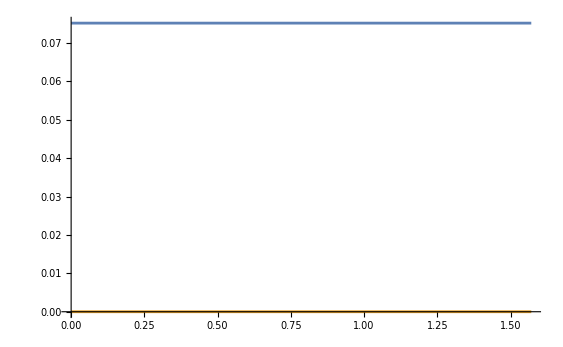

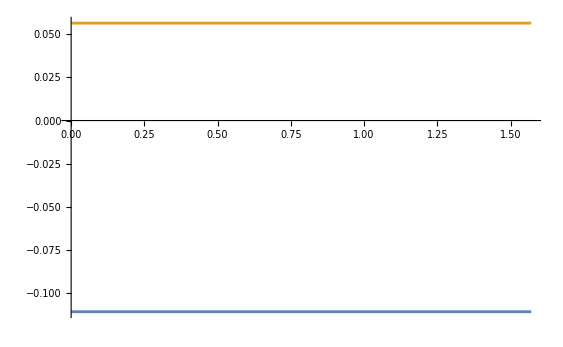

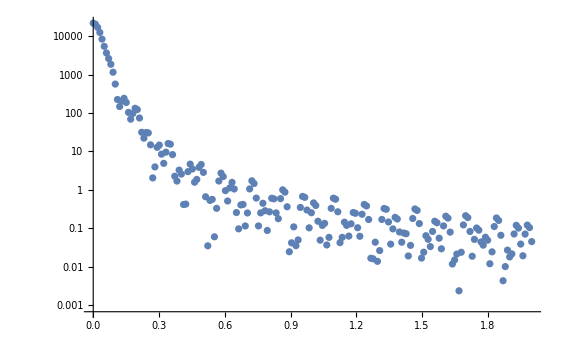

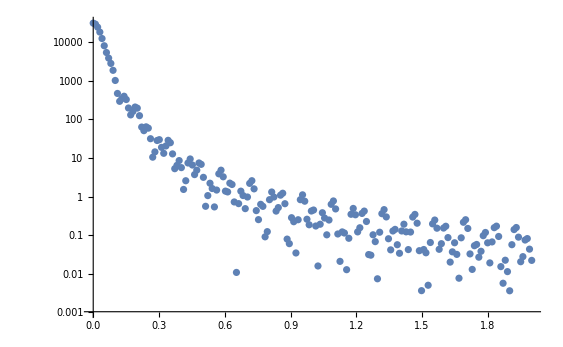

```mathematica
cppspecfolder="spec_comp_constfield_m140_varphase_20250120_094422/spec_20250120_094514";
dataspec=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/spectr.txt"],"CSV"];
dataspecanti=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/spectr_anti.txt"],"CSV"];
dataf0=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/field0.txt"],"CSV"];
datadf0=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/field0_deriv.txt"],"CSV"];

dataf0[[1;;5]]
datadf0[[1;;5]]
αf0s=Transpose[dataf0[[3;;]]][[1]];
f0Res=Transpose[dataf0[[3;;]]][[2]];
f0Ims=Transpose[dataf0[[3;;]]][[3]];
αdf0s=Transpose[datadf0[[3;;]]][[1]];
df0Res=Transpose[datadf0[[3;;]]][[2]];
df0Ims=Transpose[datadf0[[3;;]]][[3]];

dataspec[[1;;5]]
dataspecanti[[1;;5]]
dataspectemp=DeleteCases[dataspec,_?(StringMatchQ[#[[1]],"#"~~___]&)];
dataspecantitemp=DeleteCases[dataspecanti,_?(StringMatchQ[#[[1]],"#"~~___]&)];
pTscpp=Transpose[dataspectemp[[2;;]]][[1]];
speccpp=Transpose[dataspectemp[[2;;]]][[2]];
pTscppanti=Transpose[dataspecantitemp[[2;;]]][[1]];
specanticpp=Transpose[dataspecantitemp[[2;;]]][[2]];

ϕ=Interpolation[Transpose@{αf0s,f0Res+I*f0Ims}];
Dϕ=Interpolation[Transpose@{αdf0s,df0Res+I*df0Ims}];
Plot[{Re@ϕ[α],Im@ϕ[α]},{α,0,π/2}]
Plot[{Re@Dϕ[α],Im@Dϕ[α]},{α,0,π/2}]

ListLogPlot[Transpose@{pTscpp,speccpp}]
ListLogPlot[Transpose@{pTscppanti,specanticpp}]
```

Define the desired momentum grid and compute spectrum and antispectrum. For real fields the particle and antiparticle spectra are identical. The computation takes a while...

```mathematica
pTs=Range[0,2,0.01];
```

```mathematica
Jp=ComputeJp[0.14,pTs,ϕ,Dϕ,False];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained -0.0382158+0.0347091 ⅈ and 1.83351×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained -0.205539+0.0907931 ⅈ and 2.38563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained -0.00323039+0.0831583 ⅈ and 2.67118×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Jpanti=ComputeJp[0.14,pTs,ϕ,Dϕ,True];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained 0.063842+0.0394572 ⅈ and 2.27763×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained -0.00358558-0.0343001 ⅈ and 1.87651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.55627595791063}. NIntegrate obtained 0.226205+0.0313703 ⅈ and 2.68665×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

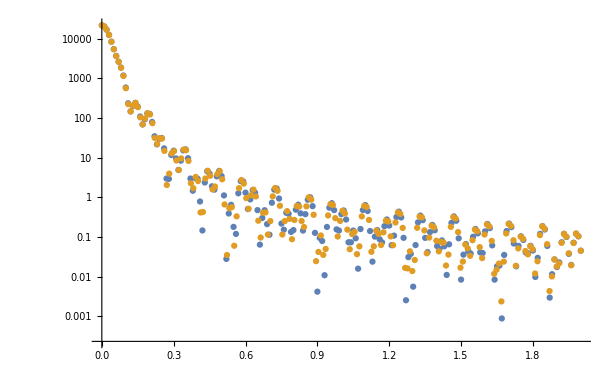

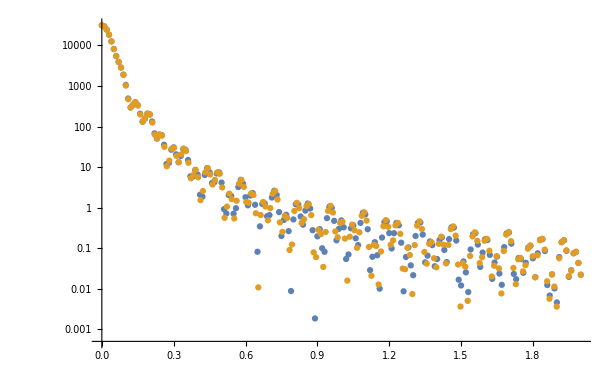

```mathematica
spectr=Abs[Jp^2]/(2*π)^3;
spectranti=Abs[Jpanti^2]/(2*π)^3;
ListLogPlot[{Transpose@{pTs,spectr},Transpose@{pTscpp,speccpp}}]
ListLogPlot[{Transpose@{pTs,spectranti},Transpose@{pTscppanti,specanticpp}}]
```